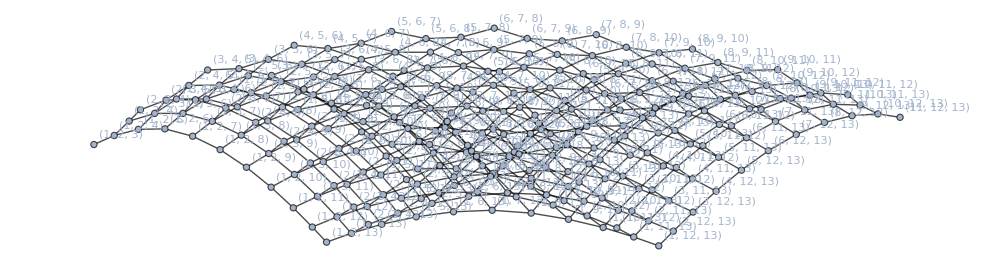

```mathematica
g=Import["C:\\Users\\Joel9\\Documents\\Investigacion Grafos\\Packing and 3token graphs\\Archivos Pn\\P13\\F3.gml"]
```

```mathematica
VertexList[g]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285}

```mathematica
m=TableForm[GraphDistanceMatrix[g],TableHeadings->{c=Style[#,Red]&/@%,c}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285
0 | 0 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 17 | 17 | 15 | 16 | 16 | 17 | 17 | 18 | 18 | 17 | 18 | 18 | 19 | 19 | 19 | 20 | 20 | 21 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 14 | 15 | 16 | 17 | 18 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 14 | 15 | 16 | 17 | 18 | 19 | 16 | 17 | 18 | 19 | 20 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 15 | 16 | 17 | 18 | 19 | 20 | 17 | 18 | 19 | 20 | 21 | 19 | 20 | 21 | 22 | 21 | 22 | 23 | 23 | 24 | 25 | 18 | 19 | 20 | 21 | 22 | 20 | 21 | 22 | 23 | 22 | 23 | 24 | 24 | 25 | 26 | 21 | 22 | 23 | 24 | 23 | 24 | 25 | 25 | 26 | 27 | 24 | 25 | 26 | 26 | 27 | 28 | 27 | 28 | 29 | 30
1 | 1 | 0 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 14 | 15 | 15 | 16 | 16 | 17 | 17 | 16 | 17 | 17 | 18 | 18 | 18 | 19 | 19 | 20 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 14 | 15 | 16 | 17 | 18 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 14 | 15 | 16 | 17 | 18 | 19 | 16 | 17 | 18 | 19 | 20 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 17 | 18 | 19 | 20 | 21 | 19 | 20 | 21 | 22 | 21 | 22 | 23 | 23 | 24 | 25 | 20 | 21 | 22 | 23 | 22 | 23 | 24 | 24 | 25 | 26 | 23 | 24 | 25 | 25 | 26 | 27 | 26 | 27 | 28 | 29
2 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 15 | 16 | 16 | 17 | 17 | 17 | 18 | 18 | 19 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 13 | 14 | 15 | 16 | 17 | 18 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 16 | 17 | 18 | 19 | 20 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 19 | 20 | 21 | 22 | 21 | 22 | 23 | 23 | 24 | 25 | 22 | 23 | 24 | 24 | 25 | 26 | 25 | 26 | 27 | 28
3 | 2 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 13 | 14 | 14 | 15 | 15 | 16 | 16 | 15 | 16 | 16 | 17 | 17 | 17 | 18 | 18 | 19 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 13 | 14 | 15 | 16 | 17 | 18 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 16 | 17 | 18 | 19 | 20 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 19 | 20 | 21 | 22 | 21 | 22 | 23 | 23 | 24 | 25 | 22 | 23 | 24 | 24 | 25 | 26 | 25 | 26 | 27 | 28
4 | 3 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 14 | 15 | 15 | 16 | 16 | 16 | 17 | 17 | 18 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 21 | 22 | 23 | 23 | 24 | 25 | 24 | 25 | 26 | 27
5 | 3 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 14 | 15 | 15 | 16 | 16 | 16 | 17 | 17 | 18 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 21 | 22 | 23 | 23 | 24 | 25 | 24 | 25 | 26 | 27
6 | 4 | 3 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 13 | 14 | 14 | 15 | 15 | 15 | 16 | 16 | 17 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 20 | 21 | 22 | 22 | 23 | 24 | 23 | 24 | 25 | 26
7 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 13 | 14 | 14 | 15 | 15 | 15 | 16 | 16 | 17 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 20 | 21 | 22 | 22 | 23 | 24 | 23 | 24 | 25 | 26
8 | 5 | 4 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 12 | 13 | 13 | 14 | 14 | 14 | 15 | 15 | 16 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
9 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 12 | 13 | 13 | 14 | 14 | 14 | 15 | 15 | 16 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
10 | 6 | 5 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 11 | 9 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 9 | 8 | 9 | 10 | 11 | 12 | 10 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
11 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
12 | 7 | 6 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 11 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 11 | 10 | 11 | 12 | 13 | 12 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
13 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 8 | 7 | 8 | 9 | 10 | 11 | 9 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
14 | 8 | 7 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 12 | 11 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 12 | 11 | 10 | 11 | 12 | 13 | 12 | 11 | 12 | 13 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 13 | 12 | 13 | 14 | 14 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
15 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
16 | 9 | 8 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 13 | 12 | 11 | 10 | 9 | 10 | 13 | 12 | 11 | 10 | 11 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 11 | 14 | 13 | 12 | 11 | 12 | 14 | 13 | 12 | 13 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 14 | 13 | 12 | 13 | 15 | 14 | 13 | 14 | 15 | 14 | 15 | 15 | 16 | 17 | 16 | 15 | 14 | 15 | 16 | 15 | 16 | 16 | 17 | 18 | 17 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
17 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 10 | 9 | 10 | 11 | 12 | 11 | 10 | 11 | 12 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 12 | 11 | 12 | 13 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
18 | 10 | 9 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 11 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 12 | 11 | 10 | 15 | 14 | 13 | 12 | 11 | 15 | 14 | 13 | 12 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 14 | 13 | 12 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 16 | 15 | 16 | 17 | 16 | 15 | 14 | 17 | 16 | 15 | 17 | 16 | 17 | 18 | 17 | 16 | 18 | 17 | 18 | 19 | 18 | 19 | 20
19 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 1 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 13 | 12 | 11 | 10 | 11 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 12 | 11 | 12 | 14 | 13 | 12 | 13 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 14 | 13 | 14 | 15 | 14 | 15 | 15 | 16 | 17 | 16 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
20 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 12 | 11 | 15 | 14 | 13 | 12 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 14 | 13 | 16 | 15 | 14 | 16 | 15 | 16 | 17 | 16 | 15 | 17 | 16 | 17 | 18 | 17 | 18 | 19
21 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 16 | 14 | 12 | 15 | 13 | 16 | 14 | 17 | 15 | 14 | 17 | 15 | 18 | 16 | 16 | 19 | 17 | 18 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 15 | 16 | 17 | 18 | 19 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 18 | 19 | 20 | 21 | 20 | 21 | 22 | 22 | 23 | 24 | 21 | 22 | 23 | 23 | 24 | 25 | 24 | 25 | 26 | 27
22 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 11 | 12 | 12 | 13 | 13 | 14 | 14 | 13 | 14 | 14 | 15 | 15 | 15 | 16 | 16 | 17 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 20 | 21 | 22 | 22 | 23 | 24 | 23 | 24 | 25 | 26
23 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 11 | 14 | 12 | 15 | 13 | 16 | 14 | 13 | 16 | 14 | 17 | 15 | 15 | 18 | 16 | 17 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 11 | 12 | 13 | 14 | 15 | 16 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 14 | 15 | 16 | 17 | 18 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 17 | 18 | 19 | 20 | 19 | 20 | 21 | 21 | 22 | 23 | 20 | 21 | 22 | 22 | 23 | 24 | 23 | 24 | 25 | 26
24 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 10 | 11 | 11 | 12 | 12 | 13 | 13 | 12 | 13 | 13 | 14 | 14 | 14 | 15 | 15 | 16 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
25 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 12 | 15 | 13 | 16 | 14 | 14 | 17 | 15 | 16 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
26 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
27 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
28 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
29 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
30 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
31 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
32 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
33 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
34 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 10 | 11 | 12 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
35 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 10 | 11 | 12 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
36 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 11 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 12 | 13 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
37 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 8 | 9 | 7 | 8 | 6 | 9 | 7 | 8 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 11 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 12 | 13 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
38 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 12 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 14 | 16 | 15 | 16 | 17 | 16 | 17 | 18
39 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 9 | 10 | 8 | 9 | 7 | 9 | 10 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 12 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 14 | 16 | 15 | 16 | 17 | 16 | 17 | 18
40 | 5 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 12 | 15 | 13 | 16 | 14 | 14 | 17 | 15 | 16 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 10 | 11 | 12 | 13 | 14 | 15 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 13 | 14 | 15 | 16 | 17 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 16 | 17 | 18 | 19 | 18 | 19 | 20 | 20 | 21 | 22 | 19 | 20 | 21 | 21 | 22 | 23 | 22 | 23 | 24 | 25
41 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
42 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
43 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
44 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
45 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
46 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
47 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
48 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
49 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
50 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
51 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
52 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 9 | 10 | 11 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
53 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
54 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 11 | 12 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
55 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 16 | 17
56 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 11 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 13 | 15 | 14 | 15 | 16 | 15 | 16 | 17
57 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
58 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
59 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
60 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
61 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
62 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
63 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
64 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
65 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
66 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
67 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
68 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
69 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
70 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 15 | 16
71 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 15 | 16
72 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
73 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 10 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
74 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
75 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
76 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
77 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
78 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
79 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
80 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
81 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
82 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
83 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 14 | 15
84 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 14 | 15
85 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
86 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 9 | 10 | 6 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
87 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
88 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
89 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
90 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
91 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
92 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
93 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
94 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
95 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
96 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 9 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
97 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 7 | 9 | 8 | 10 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 9 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 7 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
98 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
99 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 7 | 9 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
100 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
101 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
102 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
103 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
104 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
105 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
106 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 7 | 9 | 8 | 10 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 7 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 6 | 8 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 8 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
107 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
108 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 7 | 9 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 10 | 9 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
109 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 2 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
110 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 3 | 2 | 2 | 1 | 1 | 3 | 2 | 2 | 3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
111 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 4 | 2 | 3 | 1 | 3 | 4 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
112 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 0 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 7 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
113 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 8 | 10 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 7 | 9 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 6 | 8 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 0 | 2 | 1 | 3 | 1 | 2 | 2 | 3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 10 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 5 | 6 | 7 | 12 | 11 | 10 | 9 | 10 | 10 | 9 | 8 | 9 | 8 | 7 | 8 | 6 | 7 | 8 | 11 | 10 | 9 | 10 | 9 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 8 | 9 | 10 | 9 | 10 | 11 | 12
114 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 3 | 1 | 1 | 4 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
115 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 18 | 15 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 4 | 1 | 3 | 0 | 2 | 2 | 1 | 1 | 2 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 7 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 8 | 7 | 8 | 11 | 10 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11
116 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 0 | 2 | 3 | 1 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
117 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 2 | 0 | 3 | 1 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 12 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 11 | 10 | 9 | 8 | 9 | 9 | 8 | 7 | 8 | 7 | 6 | 7 | 5 | 6 | 7 | 10 | 9 | 8 | 9 | 8 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 7 | 8 | 9 | 8 | 9 | 10 | 11
118 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 19 | 16 | 18 | 15 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 17 | 14 | 16 | 13 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 15 | 12 | 14 | 11 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 3 | 0 | 2 | 1 | 18 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 15 | 14 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 10 | 9 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 5 | 14 | 13 | 12 | 11 | 10 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 8 | 7 | 6 | 13 | 12 | 11 | 10 | 11 | 10 | 9 | 9 | 8 | 7 | 12 | 11 | 10 | 10 | 9 | 8 | 11 | 10 | 9 | 10
119 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 6 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 7 | 10 | 9 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10
120 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 0 | 17 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 16 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 14 | 13 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 15 | 14 | 13 | 12 | 11 | 10 | 9 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 13 | 12 | 11 | 10 | 9 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 10 | 9 | 8 | 8 | 7 | 6 | 11 | 10 | 9 | 9 | 8 | 7 | 10 | 9 | 8 | 9
121 | 6 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 11 | 14 | 12 | 15 | 13 | 16 | 14 | 13 | 16 | 14 | 17 | 15 | 15 | 18 | 16 | 17 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 9 | 10 | 11 | 12 | 13 | 14 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 12 | 13 | 14 | 15 | 16 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 15 | 16 | 17 | 18 | 17 | 18 | 19 | 19 | 20 | 21 | 18 | 19 | 20 | 20 | 21 | 22 | 21 | 22 | 23 | 24
122 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 10 | 13 | 11 | 14 | 12 | 15 | 13 | 12 | 15 | 13 | 16 | 14 | 14 | 17 | 15 | 16 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 8 | 9 | 10 | 11 | 12 | 13 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 11 | 12 | 13 | 14 | 15 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 14 | 15 | 16 | 17 | 16 | 17 | 18 | 18 | 19 | 20 | 17 | 18 | 19 | 19 | 20 | 21 | 20 | 21 | 22 | 23
123 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
124 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
125 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
126 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
127 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 8 | 9 | 10 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
128 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 8 | 9 | 7 | 8 | 6 | 9 | 7 | 8 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 9 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 10 | 11 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
129 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 9 | 10 | 8 | 9 | 7 | 8 | 6 | 9 | 10 | 8 | 9 | 7 | 9 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 6 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 8 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 12 | 14 | 13 | 14 | 15 | 14 | 15 | 16
130 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 9 | 12 | 10 | 13 | 11 | 14 | 12 | 11 | 14 | 12 | 15 | 13 | 13 | 16 | 14 | 15 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 7 | 8 | 9 | 10 | 11 | 12 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 10 | 11 | 12 | 13 | 14 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 13 | 14 | 15 | 16 | 15 | 16 | 17 | 17 | 18 | 19 | 16 | 17 | 18 | 18 | 19 | 20 | 19 | 20 | 21 | 22
131 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 8 | 11 | 9 | 12 | 10 | 13 | 11 | 10 | 13 | 11 | 14 | 12 | 12 | 15 | 13 | 14 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
132 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
133 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
134 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
135 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 7 | 8 | 9 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
136 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 7 | 8 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 8 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 9 | 10 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
137 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 8 | 9 | 7 | 8 | 6 | 7 | 5 | 8 | 9 | 7 | 8 | 6 | 8 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 7 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 11 | 13 | 12 | 13 | 14 | 13 | 14 | 15
138 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 9 | 12 | 10 | 13 | 11 | 11 | 14 | 12 | 13 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
139 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
140 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 1 | 0 | 1 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
141 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
142 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 1 | 0 | 1 | 2 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
143 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 6 | 7 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 1 | 0 | 1 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
144 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 7 | 8 | 6 | 7 | 5 | 6 | 4 | 7 | 8 | 6 | 7 | 5 | 7 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
145 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 5 | 6 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 8 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
146 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 5 | 1 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
147 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
148 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
149 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 1 | 0 | 1 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
150 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 1 | 0 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
151 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 7 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 8 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
152 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
153 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
154 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
155 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
156 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 12 | 10 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 8 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
157 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
158 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
159 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
160 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 10 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 8 | 7 | 6 | 7 | 8 | 6 | 5 | 6 | 7

```mathematica
Export["GDM_F3(P13).csv",m]
```

GDM_F3(P13).csv